Problem 4.4.

```mathematica
Show[
ContourPlot[2y-x+4==0,{x,-1,5},{y,-3,1},PlotTheme->"Business",GridLines->Automatic],
ListPlot[{{0,-2},{4,0}}->{"A","B"},PlotStyle->Directive[Red,PointSize[0.03]]]
]
```

-Graphics-

```mathematica
x[t_]=2t+4;y[t_]=t;
Integrate[1/Sqrt[x[t]^2+y[t]^2] Sqrt[D[x[t],t]^2+D[y[t],t]^2],{t,-2,0}]
```

Log[1/2 (7+3 √5)]

Problem 4.7.

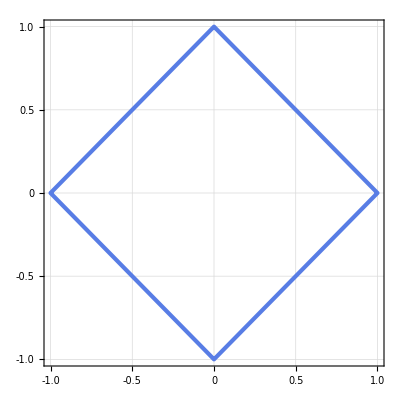

```mathematica
ContourPlot[Abs[x]+Abs[y]==1,{x,-1,1},{y,-1,1},PlotTheme->"Business",GridLines->Automatic]
```

Problem 4.26.

```mathematica
α=ArcCos[1/Sqrt[3]];
β=Pi/4;
R1[θ_]={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
R2[θ_]={{Cos[-θ],0,-Sin[-θ]},{0,1,0},{Sin[-θ],0,Cos[-θ]}};
R1[α]//MatrixForm
R2[β]//MatrixForm
```

(1/(√3) | -√(2/3) | 0
√(2/3) | 1/(√3) | 0
0 | 0 | 1)

(1/(√2) | 0 | 1/(√2)
0 | 1 | 0
-1/(√2) | 0 | 1/(√2))

```mathematica
r[t_]=R1[β].R2[α].{Cos[t],Sin[t],0};
Print["Vector normal of circle is ", R1[β].R2[α].{0,0,1}]
Print["Radius-vector function is ",r[t]]
Show[
ContourPlot3D[x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Business"],
ContourPlot3D[x+y+z==0,{x,-1,1},{y,-1,1},{z,-1,1},ContourStyle->Directive[Green,Opacity[0.5]]],
ParametricPlot3D[r[t],{t,0,2Pi},PlotStyle->Directive[Red,Thickness[0.01]]]
]
```

Vector normal of circle is {1/(√3),1/(√3),1/(√3)}

Radius-vector function is {Cos[t]/(√6)-Sin[t]/(√2),Cos[t]/(√6)+Sin[t]/(√2),-√(2/3) Cos[t]}

-Graphics3D-

```mathematica
Integrate[(r[t][[1]])^2 Sqrt[D[r[t],t].D[r[t],t]],{t,0,2Pi}]
```

(2 π)/3

Problem 5.1.

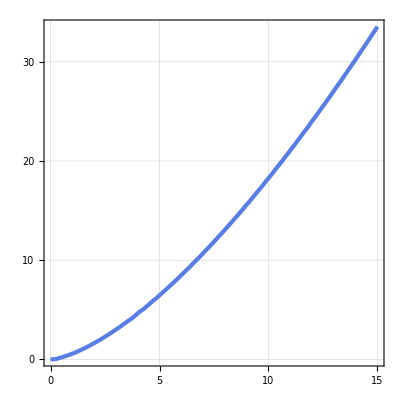

```mathematica
Clear[a];
a=3.0;
ContourPlot[a y^2==x^3,{x,0,5a},{y,0,Sqrt[(5a)^3/a]},PlotTheme->"Business",GridLines->Automatic]
```

```mathematica
Clear[a];
x[t_]=t;y[t_]=t^(3/2)/Sqrt[a];
Integrate[Sqrt[D[x[t],t]^2+D[y[t],t]^2],{t,0,5a}]
```

(335 a)/27

Problem 5.2.

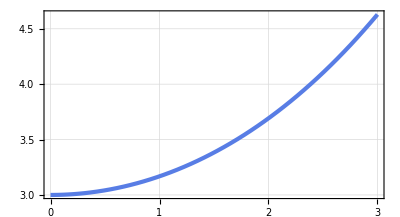

```mathematica
Clear[x,y,a];
a=3.0;
x[t_]=t;y[t_]=a/2(Exp[t/a]+Exp[-t/a]);
ParametricPlot[{x[t],y[t]},{t,0,3},PlotTheme->"Business",GridLines->Automatic]
```

```mathematica
Clear[a];
x[t_]=t;y[t_]=a/2(Exp[t/a]+Exp[-t/a]);
Assuming[x0>0&&a>0,Integrate[Sqrt[D[x[t],t]^2+D[y[t],t]^2],{t,0,x0}]]
```

a Sinh[x0/a]